```mathematica
BesselJZero[0,2]/BesselJZero[0,1]//N
```

2.29542

```mathematica
NSolve[Gamma[m] == 10.0]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{m→0.0953252}}

```mathematica
Solve[D[x^m Exp[- α^2 x^2],x] == 0,x]
```

{{x→(√m)/(√2 α)}}

```mathematica
1/(1/2 α^(-1-m) Gamma[(1+m)/2])Integrate[x^m Exp[- α^2 x^2],{x,0,Infinity}, Assumptions->{α>0,m>0}]
```

1

```mathematica
(1/(1/2 α^(-1-m) Gamma[(1+m)/2])Integrate[x^(m+1)Exp[- α^2 x^2],{x,0,Infinity}, Assumptions->{α>0,m>0}])^2
```

Gamma[1+m/2]^2/(α^2 Gamma[(1+m)/2]^2)

```mathematica
1/(1/2 α^(-1-m) Gamma[(1+m)/2])Integrate[x^(m+2)Exp[- α^2 x^2],{x,0,Infinity}, Assumptions->{α>0,m>0}]
```

Gamma[(3+m)/2]/(α^2 Gamma[(1+m)/2])

```mathematica
Simplify[Gamma[(3+m)/2]/(α^2 Gamma[(1+m)/2])-Gamma[1+m/2]^2/(α^2 Gamma[(1+m)/2]^2), Assumptions->{m>0,α>0}]
```

(-Gamma[1+m/2]^2+Gamma[(1+m)/2] Gamma[(3+m)/2])/(α^2 Gamma[(1+m)/2]^2)

```mathematica
Solve[1/Q == (√m)/(√2 α), α]
```

{{α→(√m Q)/(√2)}}

```mathematica
%17/.α-> (√m Q)/(√2)
```

(2 (-Gamma[1+m/2]^2+Gamma[(1+m)/2] Gamma[(3+m)/2]))/(m Q^2 Gamma[(1+m)/2]^2)

```mathematica
NSolve[(%19/.Q-> 1) == 2.5,m]
```

NSolve[(2 (-Gamma[1+m/2]^2+Gamma[(1+m)/2] Gamma[(3+m)/2]))/(m Gamma[(1+m)/2]^2)==2.5,m]

```mathematica
FindMinimum[Abs[(%19/.Q-> 1)-2.5],m]
FindMinimum[Abs[(%19/.Q-> 10)-2.5],{m,0.0014}]
FindMinimum[Abs[(%19/.Q-> 50)-2.5],m]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{1.16735×10^-7,{m→0.151747}}

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{5.35253×10^-6,{m→0.0014542}}

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.000129548,{m→0.0000581389}}

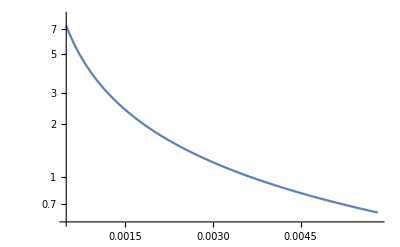

```mathematica
LogPlot[%19/.Q-> 10, {m,0.0005,0.0058138916285477293}, PlotRange->All]
```

```mathematica
(1/(1/2 α^(-1-m) Gamma[(1+m)/2])Integrate[x^m Exp[- α^2 x^2]BesselJ[0,x*q],{x,0,Infinity}, Assumptions->{α>0,m>0,q>0}])/.α-> (√m Q)/(√2)
```

LaguerreL[-1/2-m/2,-q^2/(2 m Q^2)]

```mathematica
LaguerreL[-1/2-m/2,-q^2/(2 m Q^2)]/.q-> 10/.Q-> 10/.m-> 0.0014542002798125554
```

0.0302765

```mathematica
LaguerreL[-1/2-m/2,-q^2/(2 m Q^2)]/.q-> 50/.Q-> 50/.m-> 0.000058138916285477293
```

0.00608201

```mathematica
(1/(1/2 α^(-1-m) Gamma[(1+m)/2])x^m Exp[- α^2 x^2])/.α-> (√m Q)/(√2)
```

(2^(1+1/2 (-1-m)) ⅇ^(-1/2 m Q^2 x^2) (√m Q)^(1+m) x^m)/Gamma[(1+m)/2]

```mathematica
Simplify[%69, Assumptions->{m>0,Q>0}]
```

(2^(1/2-m/2) ⅇ^(-1/2 m Q^2 x^2) √m Q (√m Q x)^m)/Gamma[(1+m)/2]

```mathematica
Simplify[(1/(1/2 α^(-1-m) Gamma[(1+m)/2])x^m Exp[- α^2 x^2])/.α-> (√m Q)/(√2), Assumptions->{m>0,Q>0}]
```

(2^(1/2-m/2) ⅇ^(-1/2 m Q^2 x^2) √m Q (√m Q x)^m)/Gamma[(1+m)/2]

```mathematica
Integrate[(2^(1/2-m/2) ⅇ^(-1/2 m Q^2 x^2) √m Q (√m Q x)^m)/Gamma[(1+m)/2] BesselJ[0,x q], {x,0,Infinity}, Assumptions->{m>0,q>0,Q>0}]
```

```mathematica
LaguerreL[1/2 (-1-m),-q^2/(2 m Q^2)]/.q-> 0/.m-> 0.15174688527548807
```

1.

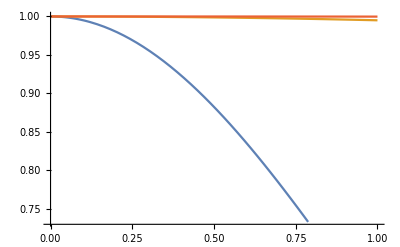

```mathematica
Plot[{LaguerreL[1/2 (-1-m),-q^2/(2 m Q^2)]/.Q-> 1/.m-> 1,LaguerreL[1/2 (-1-m),-q^2/(2 m Q^2)]/.Q-> 10/.m-> 1,,LaguerreL[1/2 (-1-m),-q^2/(2 m Q^2)]/.Q-> 50/.m-> 1}, {q,0.0,1}]
```

```mathematica
Plot[{LaguerreL[-1,-q^2/(2 m Q^2)]/.Q-> 1/.m-> 1,LaguerreL[-1,-q^2/(2 m Q^2)]/.Q-> 10/.m-> 1,,LaguerreL[-1,-q^2/(2 m Q^2)]/.Q-> 50/.m-> 1}, {q,0.0,1}]
```

-Graphics-

```mathematica
Simplify[LaguerreL[-1,x], Assumptions->{x>0}]
```

LaguerreL[-1,x]

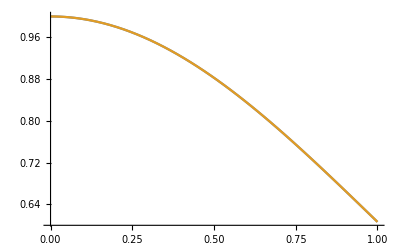

```mathematica
Plot[{LaguerreL[-1,-q^2/(2 m Q^2)]/.Q-> 1/.m-> 1,Hypergeometric1F1[1,1,-q^2/(2 m Q^2)/.m-> 1/.Q-> 1]}, {q,0,1}]
```

```mathematica
Series[Pochhammer[1,ϵ-1]/Gamma[ϵ], {ϵ, 0, 1}]
```

1+O[ϵ]^2

```mathematica
Gamma[0]
```

ComplexInfinity

```mathematica
Solve[D[x^m Exp[- α^2 x^2],x]== 0,x]
```

{{x→(√m)/(√2 α)}}

```mathematica
TeXForm[(-Gamma[1+m/2]^2+Gamma[(1+m)/2] Gamma[(3+m)/2])/(α^2 Gamma[(1+m)/2]^2)]
```

\frac{\Gamma \left(\frac{m+1}{2}\right) \Gamma \left(\frac{m+3}{2}\right)-\Gamma \left(\frac{m}{2}+1\right)^2}{\alpha ^2 \Gamma \left(\frac{m+1}{2}\right)^2}

```mathematica
TeXForm[LaguerreL[1/2 (-1-m),-q^2/(2 m Q^2)]]
```

L_{\frac{1}{2} (-m-1)}\left(-\frac{q^2}{2 m Q^2}\right)

```mathematica
1/(1/2 α^(-1-m) Gamma[(1+m)/2])Integrate[x^m Exp[- α^2 x^2]BesselJ[ν,x*q],{x,0,Infinity}, Assumptions->{α>0,m>0,q>0,ν>0}]
```

(2^-ν q^ν α^-ν Gamma[1/2 (1+m+ν)] Hypergeometric1F1Regularized[1/2 (1+m+ν),1+ν,-q^2/(4 α^2)])/Gamma[(1+m)/2]

```mathematica
TeXForm[(2^-ν q^ν α^-ν Gamma[1/2 (1+m+ν)] Hypergeometric1F1Regularized[1/2 (1+m+ν),1+ν,-q^2/(4 α^2)])/Gamma[(1+m)/2]]
```

\frac{2^{-\nu } \alpha ^{-\nu } q^{\nu } \Gamma \left(\frac{1}{2} (m+\nu +1)\right) \, _1\tilde{F}_1\left(\frac{1}{2} (m+\nu +1);\nu +1;-\frac{q^2}{4 \alpha ^2}\right)}{\Gamma
   \left(\frac{m+1}{2}\right)}